# The N=2 characteristic polynomial

## Study the behavior of λ with q-ratio

```mathematica
matEl[n_,m_,e_,v_]:=Piecewise[{{n*e, n==m}, {Sqrt[m+1]Sqrt[m+2](-v), n-m==2}, {Sqrt[m]Sqrt[m-1](-v), n-m==-2}}];
Hmat02[n_,e_,v_]:=Table[Table[matEl[2(i-1),2(j-1),e,v],{j,1,n}],{i,1,n}];
Hmat13[n_,e_,v_]:=Table[Table[matEl[2i+1,2j+1,e,v],{j,0,n-1}],{i,0,n-1}];
```

```mathematica
boson0[n_]:=Hmat02[n,1,q];
boson1[n_]:=Hmat13[n,1,q];
function[q_,n_]:=Table[Eigenvalues[boson0[n]][[id]],{id,1,Length[Eigenvalues[boson0[n]]]}];
```

```mathematica
sol[n_,p_]:=Eigenvalues[boson0[n]]/.{q->p};
```

```mathematica
N[sol[10,1]]
```

{-11.6496,-5.83432,-2.09878,-0.170188,2.40978,6.55402,12.0478,19.1292,28.3619,41.2502}

```mathematica
proc[t_]:=Do[Print[N[sol[n,p]/.{p->t}]],{n,2,10,1}];
```

```mathematica
proc[0]
```

{0.,2.}

{0.,2.,4.}

{0.,2.,4.,6.}

{0.,2.,4.,6.,8.}

{0.,2.,4.,6.,8.,10.}

{0.,2.,4.,6.,8.,10.,12.}

{0.,2.,4.,6.,8.,10.,12.,14.}

{0.,2.,4.,6.,8.,10.,12.,14.,16.}

{0.,2.,4.,6.,8.,10.,12.,14.,16.,18.}

```mathematica
proc[1]
```

{-0.732051,2.73205}

{-1.50664,0.79062,6.71602}

{-2.60849,-0.115564,3.56838,11.1557}

{-3.93442,-0.708168,1.75028,7.03444,15.8579}

{-5.37042,-1.36446,0.581418,4.53464,10.8839,20.7349}

{-6.87512,-2.25934,-0.150887,2.76847,7.78012,14.9986,25.7381}

{-8.43005,-3.35037,-0.696095,1.45047,5.53683,11.3416,19.3101,30.8375}

{-10.0241,-4.55473,-1.2991,0.489412,3.80059,8.65898,15.1414,23.7746,36.0129}

{-11.6496,-5.83432,-2.09878,-0.170188,2.40978,6.55402,12.0478,19.1292,28.3619,41.2502}

```mathematica
proc[2]
```

{-2.,4.}

{-4.96523,0.623166,10.3421}

{-8.87738,-1.11211,4.4302,17.5593}

{-13.1966,-3.16645,1.28354,9.82974,25.2498}

{-17.7533,-6.11036,-0.485867,5.11985,15.9761,33.2536}

{-22.477,-9.59086,-2.13717,2.00264,10.1105,22.6089,41.4829}

{-27.3267,-13.3751,-4.47242,0.0811008,5.88795,15.7226,29.5988,49.8838}

{-32.2753,-17.3765,-7.42458,-1.40627,2.7736,10.6449,21.7795,36.8646,58.4201}

{-37.3042,-21.5472,-10.725,-3.30505,0.660508,6.6906,15.9307,28.1819,44.3511,67.0667}

```mathematica
proc[3]
```

{-3.3589,5.3589}

{-8.63355,0.594005,14.0395}

{-15.3364,-2.18925,5.48605,24.0396}

{-22.6493,-6.03858,1.18129,12.7825,34.724}

{-30.3365,-11.3124,-1.43296,5.99399,21.2283,45.8596}

{-38.2897,-17.3237,-4.56589,1.78756,12.6872,30.3849,57.3197}

{-46.4438,-23.7918,-9.00155,-0.816642,6.61979,20.3489,40.059,69.0261}

{-54.7562,-30.5988,-14.2424,-3.51907,2.42242,12.9681,28.6668,50.1318,80.9272}

{-63.1969,-37.6728,-19.9666,-7.34955,-0.259196,7.29987,20.1465,37.489,60.5231,92.9866}

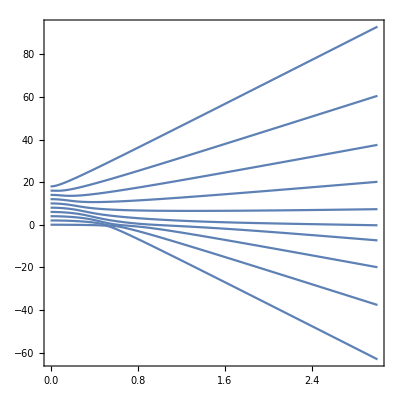

```mathematica
Plot[sol[10,p],{p,0,3},AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->Automatic]
```

```mathematica
b04=boson0[4]/.{q->1};
```

## Compute the normalization of the eigenvectors of a squared Matrix

```mathematica
vectors[m_]:=Eigenvectors[m];
vectorsN[m_]:=Table[Normalize[vectors[m][[Length[vectors[m]]-id]]],{id,0,Length[vectors[m]]-1}];
values[m_]:=Eigenvalues[m];
```

```mathematica
N[values[b04]]
```

{11.1557,3.56838,-2.60849,-0.115564}

```mathematica
Eigenvalues[N[boson0[4]/.{q->1/2}]]
```

{8.08864,3.42696,0.839097,-0.354696}

```mathematica
N[vectorsN[b04]]
```

{{-0.898719,-0.0734401,0.32205,0.288435},{0.311885,0.575267,0.637984,0.405922},{0.306565,-0.773533,0.225065,0.506961},{-0.0324,0.25558,-0.662274,0.703579}}

```mathematica
v1
```

{-0.0460503,0.363257,-0.941293,1.}

```mathematica
Transpose[N[vectorsN[b04]]]//MatrixForm
```

(-0.0324 | 0.306565 | 0.311885 | -0.898719
0.25558 | -0.773533 | 0.575267 | -0.0734401
-0.662274 | 0.225065 | 0.637984 | 0.32205
0.703579 | 0.506961 | 0.405922 | 0.288435)

```mathematica
v1N=vectorsN[v1]
```

Eigenvectors::matsq: Argument {-0.0460503,0.363257,-0.941293,1.} at position 1 is not a non-empty square matrix.

Part::partw: Part 2 of Eigenvectors[{-0.0460503,0.363257,-0.941293,1.}] does not exist.

Eigenvectors::matsq: Argument {-0.0460503,0.363257,-0.941293,1.} at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvectors::matsq will be suppressed during this calculation.

Part::partw: Part 3 of Eigenvectors[{-0.0460503,0.363257,-0.941293,1.}] does not exist.

Part::partw: Part 4 of Eigenvectors[{-0.0460503,0.363257,-0.941293,1.}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.0324,0.25558,-0.662274,0.703579},Normalize[Eigenvectors[{-0.0460503,0.363257,-0.941293,1.}]⟦2⟧],Normalize[Eigenvectors[{-0.0460503,0.363257,-0.941293,1.}]⟦3⟧],Normalize[Eigenvectors[{-0.0460503,0.363257,-0.941293,1.}]⟦4⟧]}

```mathematica
v1.v1/(Norm[v1]^2)
```

1.

```mathematica
v1N.v1N
```

1.

```mathematica
N[boson1[3]/.{q->1}]//MatrixForm
```

(1. | -2.44949 | 0.
-2.44949 | 3. | -4.47214
0. | -4.47214 | 5.)

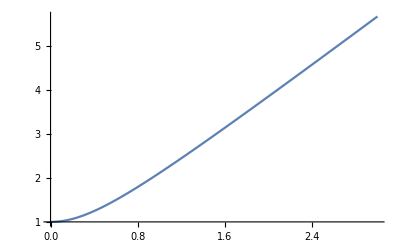

```mathematica
Plot[√(1+2 √3 q^2),{q,0,3}]
```

```mathematica
proc[n_]:=Manipulate[Plot[function[q,n][[id]],{q,0,3}],{id,1,Length[Eigenvalues[boson0[n]]],1}];
```

### The solutions λ_i of H_nwith a fixed n

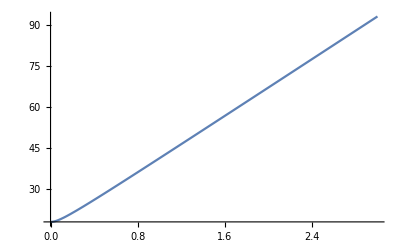
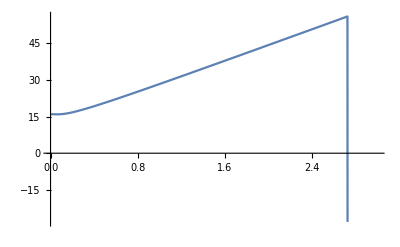
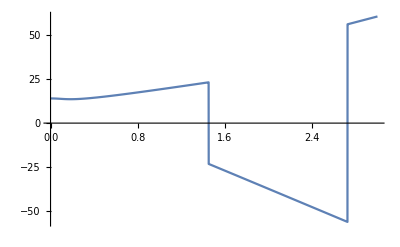
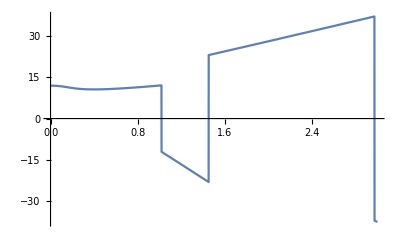
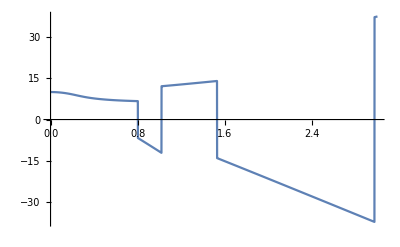
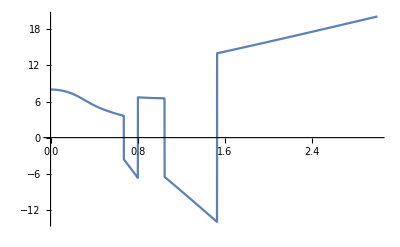
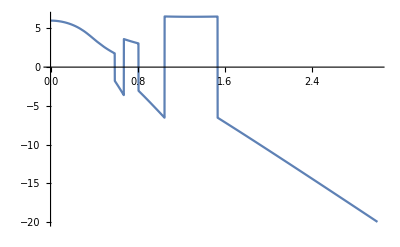
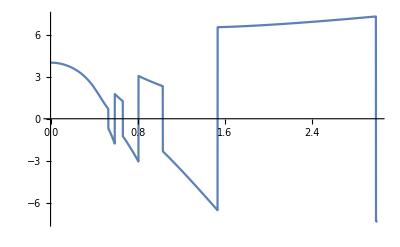

```mathematica
Table[Plot[function[q,10][[id]],{q,0,3}],{id,1,Length[Eigenvalues[boson0[10]]],1}]
```

## q=1, Numerical example: solutions

```mathematica
N[Eigenvalues[boson0[10]]/.{q->1.2}]
```

{-16.7246,-8.88007,-3.66803,-0.685819,1.88377,6.49895,12.7628,20.8926,31.526,46.3944}

```mathematica
N[Eigenvalues[boson0[9]]/.{q->1.2}]
```

{-14.4204,-7.02484,-2.34029,0.0407015,3.49194,8.99424,16.4229,26.3598,40.4759}

```mathematica
N[Eigenvalues[boson0[8]]/.{q->1.2}]
```

{-12.1576,-5.26187,-1.29381,1.03398,5.54168,12.1724,21.3362,34.6291}

```mathematica
N[Eigenvalues[boson0[7]]/.{q->1.2}]
```

{-9.94604,-3.62532,-0.512726,2.52284,8.20101,16.4901,28.8702}

```mathematica
N[Eigenvalues[boson0[6]]/.{q->1.2}]
```

{-7.79993,-2.19897,0.300783,4.6028,11.8728,23.2226}

```mathematica
f610[q_]:=Eigenvalues[boson0[10]/.{q->1.2}][[6]];
f69[q_]:=Eigenvalues[boson0[9]/.{q->1.2}][[6]];
f68[q_]:=Eigenvalues[boson0[8]/.{q->1.2}][[6]];
f67[q_]:=Eigenvalues[boson0[7]/.{q->1.2}][[6]];
f66[q_]:=Eigenvalues[boson0[6]/.{q->1.2}][[6]];
```

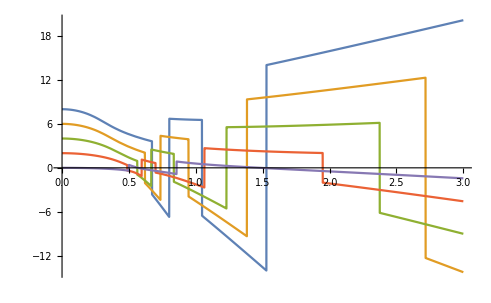

```mathematica
Plot[{f610[q],f69[q],f68[q],f67[q],f66[q]},{q,0,3}]
```

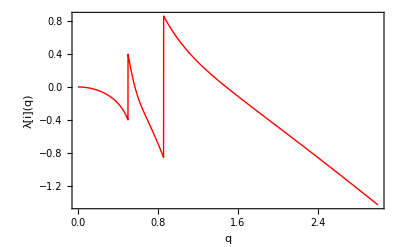

```mathematica
Plot[function[q,6][[6]],{q,0,3},Axes -> False, Frame -> True, 
 PlotRange -> {Full, Full}, PlotStyle->{Red,Thick},
 FrameLabel -> {"q","λ[i](q)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"}]
```

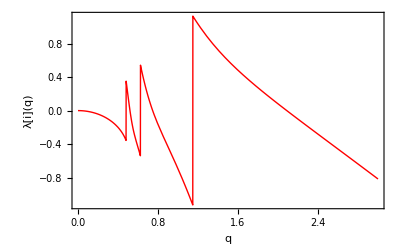

```mathematica
Plot[function[q,8][[8]],{q,0,3}, Axes -> False, Frame -> True, 
 PlotRange -> {Full, Full}, PlotStyle->{Red,Thick},
 FrameLabel -> {"q","λ[i](q)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"}]
```